# eFC: Pearson on Neural Data

```mathematica
SetDirectory[NotebookDirectory[]];
cd=ColorData[97,"ColorList"];
dir ="../AnalysisData/best_categ_pass_agent/";
```

```mathematica
aa=Flatten[Import[StringJoin[dir,"efc_efc_A_avoid_unclustered.dat"]]];
ac=Flatten[Import[StringJoin[dir,"efc_efc_A_pass_unclustered.dat"]]];
ba=Flatten[Import[StringJoin[dir,"efc_efc_B_avoid_unclustered.dat"]]];
bc=Flatten[Import[StringJoin[dir,"efc_efc_B_catch_unclustered.dat"]]];
```

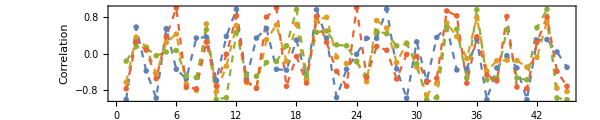

SubtaskMIe.eps

```mathematica
ListLinePlot[{ba,bc,aa,ac},AspectRatio->1/5,PlotMarkers->{●},PlotStyle->Dashed,PlotRange->All,Frame->True,ImageSize->600,FrameLabel->{"Edge Pairs","Correlation"}]
Export["SubtaskMIe.eps",%]
```

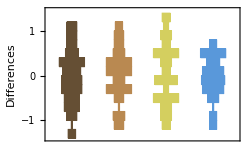

SubtaskCosFC_hist.eps

```mathematica
DistributionChart[{ba-bc,aa-ac,ba-aa,bc-ac},ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",PlotRange->All,FrameLabel->{"","Differences"},Frame->True,ImageSize->250]
Export["SubtaskCosFC_hist.eps",%]
```

```mathematica
{CosineDistance[ba,bc],CosineDistance[aa,ac],CosineDistance[ba,aa],CosineDistance[bc,ac]}
```

{0.51225529630176217,0.38404085424190291,0.63264784700569683,0.23621940573711009}

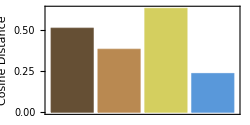

SubtaskCosFC.eps

```mathematica
BarChart[{CosineDistance[ba,bc],CosineDistance[aa,ac],CosineDistance[ba,aa],CosineDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Cosine Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},Automatic},Frame->True,ImageSize->250]
Export["SubtaskCosFC.eps",%]
```

```mathematica
{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac]}
```

{3.720892342067931,3.5054306725923299,4.2495844364159963,2.719349919048205}

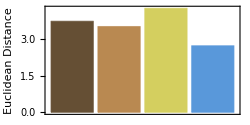

SubtaskEucFC_NA.eps

```mathematica
BarChart[{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Euclidean Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},All},Frame->True,ImageSize->250]
Export["SubtaskEucFC_NA.eps",%]
```

# eFC: Pearson on MI

```mathematica
SetDirectory[NotebookDirectory[]];
cd=ColorData[97,"ColorList"];
dir ="../AnalysisData/best_categ_pass_agent/";
```

```mathematica
aa=Flatten[Import[StringJoin[dir,"efc_mi_A_avoid.dat"]]];
ac=Flatten[Import[StringJoin[dir,"efc_mi_A_pass.dat"]]];
ba=Flatten[Import[StringJoin[dir,"efc_mi_B_avoid.dat"]]];
bc=Flatten[Import[StringJoin[dir,"efc_mi_B_catch.dat"]]];
```

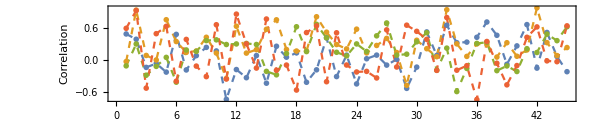

SubtaskMIe.eps

```mathematica
ListLinePlot[{ba,bc,aa,ac},AspectRatio->1/5,PlotMarkers->{●},PlotStyle->Dashed,PlotRange->All,Frame->True,ImageSize->600,FrameLabel->{"Edge Pairs","Correlation"}]
Export["SubtaskMIe.eps",%]
```

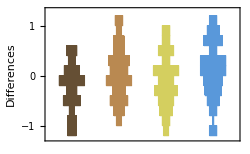

SubtaskCosFC_hist.eps

```mathematica
DistributionChart[{ba-bc,aa-ac,ba-aa,bc-ac},ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",PlotRange->All,FrameLabel->{"","Differences"},Frame->True,ImageSize->250]
Export["SubtaskCosFC_hist.eps",%]
```

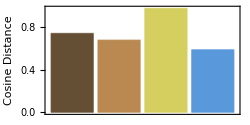

SubtaskCosFC.eps

```mathematica
BarChart[{CosineDistance[ba,bc],CosineDistance[aa,ac],CosineDistance[ba,aa],CosineDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Cosine Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},Automatic},Frame->True,ImageSize->250]
Export["SubtaskCosFC.eps",%]
```

```mathematica
{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac]}
```

{3.1743099624548748,3.259579205193213,3.2245083128136,3.271857078913768}

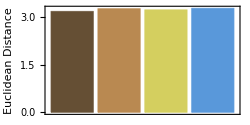

SubtaskEucFC_MI.eps

```mathematica
BarChart[{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Euclidean Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},All},Frame->True,ImageSize->250]
Export["SubtaskEucFC_MI.eps",%]
```